## Lesson

List numbers within range and with step:

```mathematica
Range[10,20,2]
```

{10,12,14,16,18,20}

List expressions with n within range and with step:

```mathematica
Table[f[n],{n,2,10,4}]
```

{f[2],f[6],f[10]}

list of 20 random integers up to 10:

```mathematica
RandomInteger[10,20]
```

{4,10,6,4,0,0,5,10,10,4,5,5,0,8,1,5,7,3,3,1}

## Questions

Q1. Make a list in which the number 1000 is repeated 5 times.

```mathematica
Table[1000,5]
```

{1000,1000,1000,1000,1000}

Q2. Make a table of the values of n^3 for n from 10 to 20.

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

Q3. Make a number line plot of the first 20 squares.

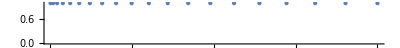

```mathematica
NumberLinePlot[Range[20]^2]
```

Q4. Make a list of the even numbers (2, 4, 6, ...) up to 20.

```mathematica
2Range[10]
```

{2,4,6,8,10,12,14,16,18,20}

Q5. Use Table to get the same result as Range[10].

```mathematica
Table[i,{i,10}]
```

{1,2,3,4,5,6,7,8,9,10}

Q6. Make a bar chart of the first 10 squares.

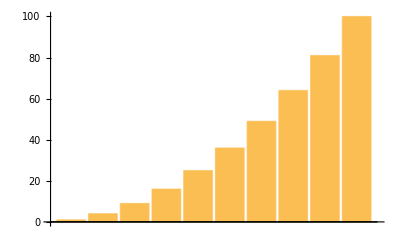

```mathematica
BarChart[Range[10]^2]
```

Q7. Make a table of lists of digits for the first 10 squares.

```mathematica
Table[IntegerDigits[i^2],{i,10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

Q8. Make a list line plot of the length of the sequence of digits for each of the first 100 squares.

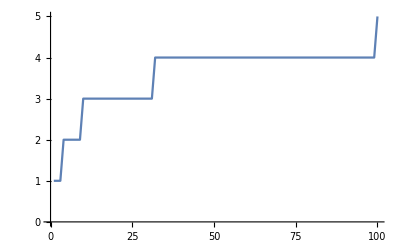

```mathematica
ListLinePlot[Table[Length[IntegerDigits[i^2]],{i,100}]]
```

Q9. Make a table of the first digit of the first 20 squares.

```mathematica
Table[First[IntegerDigits[i^2]],{i,20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

Q10. Make a list line plot of the first digits of the first 100 squares.

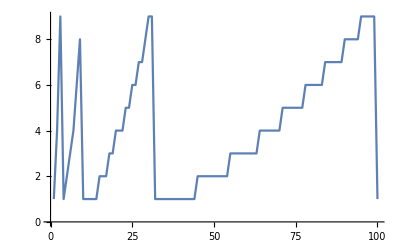

```mathematica
ListLinePlot[Table[First[IntegerDigits[i^2]],{i,100}]]
```

## Extended Questions

+Q1. Make a list of the differences between n^3 and n^2 with n up to 10.

```mathematica
Range[10]^3-Range[10]^2
```

{0,4,18,48,100,180,294,448,648,900}

+Q2. Make a list of the odd numbers (1, 3, 5, ...) up to 100.

```mathematica
2Range[50]-1
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

+Q3. Make a list of the squares of even numbers up to 100.

```mathematica
(2Range[50])^2
```

{4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000}

+Q4. Create the list {-3, -2, -1, 0, 1, 2} using Range.

```mathematica
Range[-3,2]
```

{-3,-2,-1,0,1,2}

+Q5. Make a list for numbers n up to 20 in which each element is a column of the values of n, n^2 and n^3.

```mathematica
Table[Column[Range[20]^i],{i,3}]
```

{1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20,1
4
9
16
25
36
49
64
81
100
121
144
169
196
225
256
289
324
361
400,1
8
27
64
125
216
343
512
729
1000
1331
1728
2197
2744
3375
4096
4913
5832
6859
8000}

+Q6. Make a list line plot of the last digits of the first 100 squares.

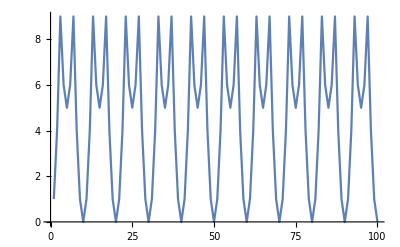

```mathematica
ListLinePlot[Table[Last[IntegerDigits[i^2]],{i,100}]]
```

+Q7. Make a list line plot of the first digit of the first 100 multiples of 3.

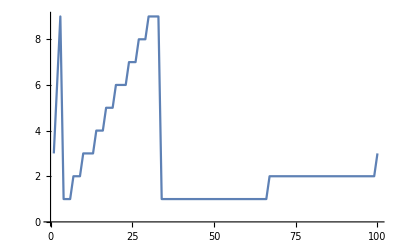

```mathematica
ListLinePlot[Table[First[IntegerDigits[3i]],{i,100}]]
```

+Q8. Make a list line plot of the total of the digits for each number up to 200.

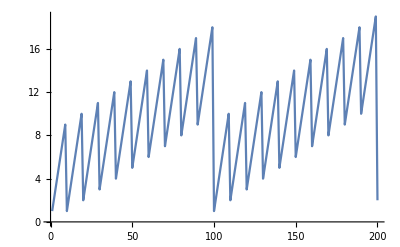

```mathematica
ListLinePlot[Table[Total[IntegerDigits[i]],{i,200}]]
```

+Q9. Make a list line plot of the total of the digits for each of the first 100 squares.

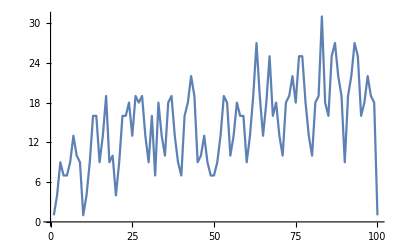

```mathematica
ListLinePlot[Table[Total[IntegerDigits[i^2]],{i,100}]]
```

+Q10. Make a number line plot of the numbers 1/n with n from 1 to 20.

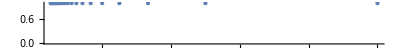

```mathematica
NumberLinePlot[1/Range[20]]
```

+Q11. Make a line plot of a list of 100 random integers where the nth integer is between 0 and n.

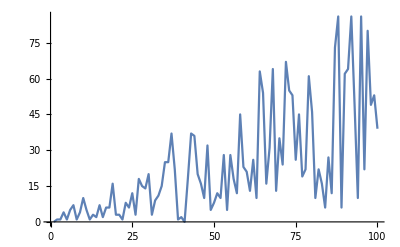

```mathematica
ListLinePlot[Table[RandomInteger[n],{n,100}]]
```